```mathematica
SIMFULLY=True;
```

```mathematica
(*Needs["PacletManager`"]
PacletInstall[NotebookDirectory[]<>"packages/MaTeX-1.7.4.paclet"]*)
```

```mathematica
Needs["MaTeX`"]
MaTeX["x^2"]
```

-Graphics-

# baseline simulation

## simulation

```mathematica
Module[{},
Clear[SIMNOTPERFECTMODEL,FASTTRAJECTORY,ESTIMATESENSITIVITY,SIMTIMEVARYINGWIND,ESTIMATESENSITIVITY2,FASTTRAJECTORY2];
If[#==1,
(*option 1*)
nameSIM="default"
];
If[#==2,
(*option 2*)
SIMNOTPERFECTMODEL=True;
nameSIM="model mismatch";
];
If[#==3,
(*option 3*)
FASTTRAJECTORY=True;
nameSIM="fast trajectory";
];
If[#==4,
(*option 4*)
ESTIMATESENSITIVITY=True;
nameSIM="estimate sensitivity";
];

If[#==5,
(*option 5*)
SIMTIMEVARYINGWIND=True;
nameSIM="time varying wind";
];

If[#==6,
(*option 6*)
ESTIMATESENSITIVITY2=True;
nameSIM="estimate sensitivity 2";
];

If[#==7,
(*option 7*)
FASTTRAJECTORY2=True;
nameSIM="fast trajectory 2";
];
]&[1]
nameSIM
```

default

```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"model_and_change_of_coordinates.nb"}]]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"backstepping_steps.nb"}]]
(*Play[Sin[440 2Pi t],{t,0,1}](*Beep[]*)*)
```

## Import

```mathematica
stateList=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_state.mx"];
estimatorsList=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_estimators.mx"];inputList=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_input.mx"];
stateStarList=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_statestar.mx"];
inputStarList=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_inputstar.mx"];
tensionsList=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_tension.mx"];
VList=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_V.mx"];
WList=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_W.mx"];
```

## some important data

```mathematica
stepsize=0.005;
TFINAL=35;
NN=Length[stateList];
XTicksLabels=Table[{Round[1/stepsize]i+1,i},{i,0,TFINAL,2}];
```

## test plotting options

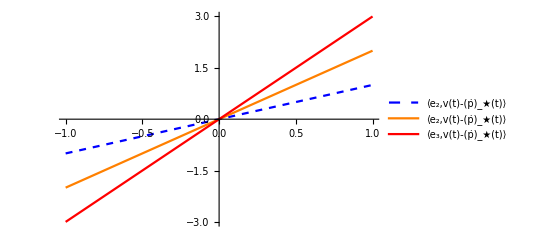

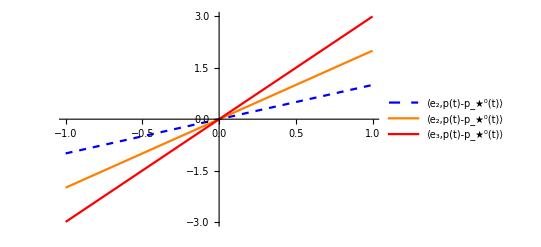

```mathematica
Plot[
{x,2x,3x},{x,-1,1},
PlotStyle-> {
{Blue,Dashed},
{Orange},
{Red}
},
PlotLegends->Placed[
{
ToExpression["\\langle e_{2}, v(t) - \dot{p}_{\\scriptscriptstyle{\\star}}(t)\\rangle",TeXForm,HoldForm],
ToExpression["\\langle e_{2}, v(t) - \dot{p}_{\\scriptscriptstyle{\\star}}(t)\\rangle",TeXForm,HoldForm],
ToExpression["\\langle e_{3}, v(t) - \dot{p}_{\\scriptscriptstyle{\\star}}(t)\\rangle",TeXForm,HoldForm]
},{Right,Top}]
] 
Plot[
{x,2x,3x},{x,-1,1},
PlotStyle-> {
{Blue,Dashed},
{Orange},
{Red}
},
PlotLegends->Placed[
{
ToExpression["\\langle e_{2}, p(t) - p_{\\scriptscriptstyle{\\star}}^{\\scriptscriptstyle{(0)}}(t)\\rangle",TeXForm,HoldForm],
ToExpression["\\langle e_{2}, p(t) - p_{\\scriptscriptstyle{\\star}}^{\\scriptscriptstyle{(0)}}(t)\\rangle",TeXForm,HoldForm],
ToExpression["\\langle e_{3}, p(t) - p_{\\scriptscriptstyle{\\star}}^{\\scriptscriptstyle{(0)}}(t)\\rangle",TeXForm,HoldForm]
},{Right,Top}]
]
```

```mathematica
Needs["PacletManager`"]
PacletInstall["~/Downloads/MaTeX-1.7.4.paclet"]
```

PacletInstall::samevers: A paclet named MaTeX with the same version number (1.7.4) is already installed. Use PacletUninstall to remove the existing version first, or call PacletInstall with IgnoreVersion->True.

$Failed

```mathematica
Needs["MaTeX`"]
MaTeX["x^2"]
```

-Graphics-

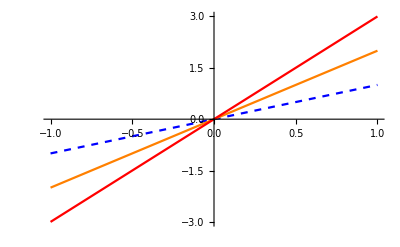

-Graphics-

```mathematica
Plot[
{x,2x,3x},{x,-1,1},
PlotStyle-> {
{Blue,Dashed},
{Orange},
{Red}
},
PlotLegends->Placed[
{
MaTeX["\|u(t) - u_{\\star,+}(t)\|"],
MaTeX["\|z(t) - z_{\\star,+}(t)\|"]
},{Right,Top}]
] 
Plot[
{x,2x,3x},{x,-1,1},
PlotStyle-> {
{Blue,Dashed},
{Orange},
{Red}
},
PlotLegends->Placed[
{
MaTeX["\\langle e_{1}, p(t) - p_{\\star}^{\\scriptscriptstyle{(0)}}(t) \\rangle \\text{(m)}"],
MaTeX["\\langle e_{1}, p(t) - p_{\\star}^{(0)}(t) \\rangle \\text{(m)}"]
},{Right,Top}]
]
```

```mathematica
ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
ColorData[97,"ColorList"]//InputForm
```

{RGBColor[0.368417, 0.506779, 0.709798], RGBColor[0.880722, 0.611041, 0.142051], RGBColor[0.560181, 0.691569, 0.194885], 
 RGBColor[0.922526, 0.385626, 0.209179], RGBColor[0.528488, 0.470624, 0.701351], RGBColor[0.772079, 0.431554, 0.102387], 
 RGBColor[0.363898, 0.618501, 0.782349], RGBColor[1, 0.75, 0], RGBColor[0.647624, 0.37816, 0.614037], 
 RGBColor[0.571589, 0.586483, 0.], RGBColor[0.915, 0.3325, 0.2125], RGBColor[0.40082222609352647, 0.5220066643438841, 
  0.85], RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142], 
 RGBColor[0.736782672705901, 0.358, 0.5030266573755369], RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

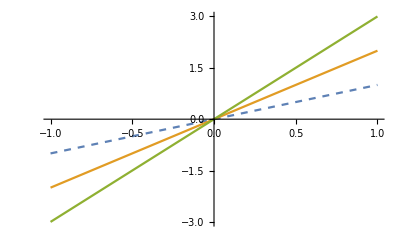

```mathematica
Plot[
{x,2x,3x},{x,-1,1},
PlotStyle-> {
{RGBColor[0.368417,0.506779,0.709798],Dashed},
{RGBColor[0.880722,0.611041,0.142051]},
{RGBColor[0.560181,0.691569,0.194885]}
},
PlotLegends->Placed[
{
MaTeX["\\langle e_{1}, p(t) - p_{\\star}^{\\scriptscriptstyle{(0)}}(t) \\rangle \\text{(m)}"],
MaTeX["\\langle e_{1}, p(t) - p_{\\star}^{(0)}(t) \\rangle \\text{(m)}"]
},{Right,Top}]
]
```

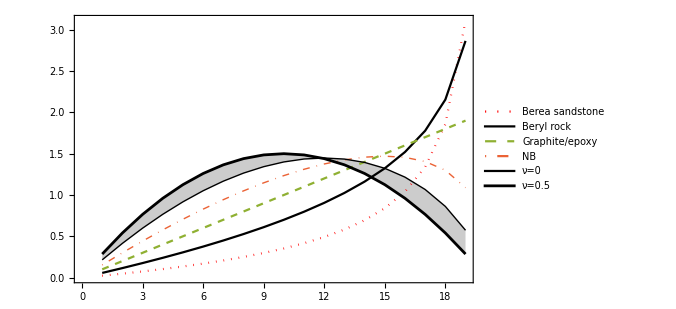

```mathematica
ListLinePlot[
Table[PDF[BetaDistribution[2,j/3],i],{j,1,6,1},{i,0.05,0.95,0.05}],
Filling->{5->{6}},
Frame->True,
RotateLabel->False,
PlotStyle->{{Dotted,Red},Black,Dashed,{DotDashed,Thick},{Black,Thick},{Black,AbsoluteThickness[2]}},
PerformanceGoal->"Quality",PlotLegends->Placed[LineLegend[Automatic,{"Berea sandstone","Beryl rock","Graphite/epoxy","NB","ν=0","ν=0.5"},Spacings->0.15],{0.2,0.8}],ImageSize->500
]
```

## position and velocity

```mathematica
errorp:= stateList[[1;;NN,{1,2,3}]]-Table[pd[stepsize (i-1)],{i,1,Length[stateList[[;;,1]]]}];
errorv:= stateList[[1;;NN,{7,8,9}]]-Table[vd[stepsize (i-1)],{i,1,Length[stateList[[;;,1]]]}];
```

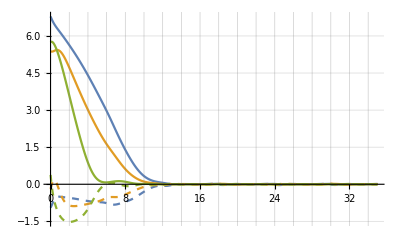
-Graphics--Graphics-

```mathematica
If[SIMFULLY,
Labeled[
ListLinePlot[{
errorp[[;;,1]],errorp[[;;,2]],errorp[[;;,3]],
errorv[[;;,1]],errorv[[;;,2]],errorv[[;;,3]]
},
PlotStyle-> {
{RGBColor[0.368417,0.506779,0.709798]},
{RGBColor[0.880722,0.611041,0.142051]},
{RGBColor[0.560181,0.691569,0.194885]},
{RGBColor[0.368417,0.506779,0.709798], Dashed},
{RGBColor[0.880722,0.611041,0.142051], Dashed},
{RGBColor[0.560181,0.691569,0.194885], Dashed}
},
PlotLegends->Placed[LineLegend[Automatic,
{
MaTeX["\\langle e_{1}, p^{\\scriptscriptstyle{(0)}}(t) - p_{\\star}^{\\scriptscriptstyle{(0)}}(t) \\rangle \\text{(m)}"],
MaTeX["\\langle e_{2}, p^{\\scriptscriptstyle{(0)}}(t) - p_{\\star}^{\\scriptscriptstyle{(0)}}(t) \\rangle \\text{(m)}"],
MaTeX["\\langle e_{3}, p^{\\scriptscriptstyle{(0)}}(t) - p_{\\star}^{\\scriptscriptstyle{(0)}}(t) \\rangle \\text{(m)}"],
MaTeX["\\langle e_{1}, p^{\\scriptscriptstyle{(1)}}(t) - p_{\\star}^{\\scriptscriptstyle{(1)}}(t) \\rangle \\text{(m/s)}"],
MaTeX["\\langle e_{2}, p^{\\scriptscriptstyle{(1)}}(t) - p_{\\star}^{\\scriptscriptstyle{(1)}}(t) \\rangle \\text{(m/s)}"],
MaTeX["\\langle e_{3}, p^{\\scriptscriptstyle{(1)}}(t) - p_{\\star}^{\\scriptscriptstyle{(1)}}(t) \\rangle \\text{(m/s)}"]
},
Spacings->0.2],
{Right,Top}
],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{MaTeX["\\text{Time (s)}"]},{Bottom,Left},RotateLabel->True
]
]
```

```mathematica
If[SIMFULLY,Export[NotebookDirectory[]<>"final_figures/sim_baseline_error_position_velocity.pdf",%];]
```

## errors to equilibrium

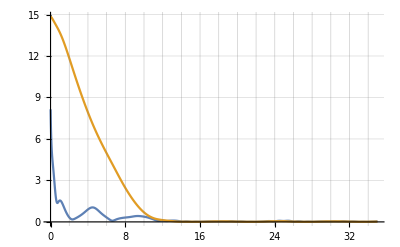
-Graphics--Graphics-

```mathematica
If[SIMFULLY,
Labeled[
ListLinePlot[{
Map[Norm,inputList-inputStarList],
Map[Norm,stateList-stateStarList]
},
PlotLegends->Placed[
{
MaTeX["\|u(t) - u_{\\star +}(t)\|"],
MaTeX["\|z(t) - z_{\\star +}(t)\|"]
},
{Right,Top}
],
PlotLegends->Placed[{"|u-u^*|","|z-z^*|"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{MaTeX["\\text{Time (s)}"]},{Bottom,Left},RotateLabel->True
]
]
```

```mathematica
If[SIMFULLY,Export[NotebookDirectory[]<>"final_figures/sim_baseline_errors.pdf",%];]
```

## Input and cable tension

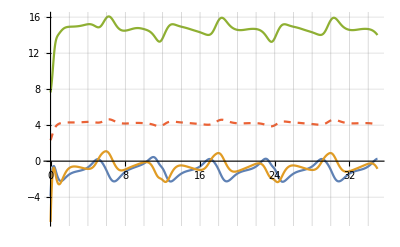
-Graphics--Graphics--Graphics-

```mathematica
If[SIMFULLY,
Labeled[
ListLinePlot[{
inputList[[;;,1]],
inputList[[;;,2]],
inputList[[;;,3]],
tensionsList
},
PlotStyle-> {
{RGBColor[0.368417,0.506779,0.709798]},
{RGBColor[0.880722,0.611041,0.142051]},
{RGBColor[0.560181,0.691569,0.194885]},
{RGBColor[0.922526,0.385626,0.209179], Dashed}
},
PlotLegends->Placed[LineLegend[Automatic,
{
MaTeX["\\langle e_{1}, u(t) \\rangle"],
MaTeX["\\langle e_{2}, u(t) \\rangle"],
MaTeX["\\langle e_{3}, u(t) \\rangle"],
MaTeX["T(z(t), u(t))"]
},
Spacings->0.15],
{0.85,0.7}
],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{MaTeX["\\text{Time (s)}"],MaTeX["\\text{(N)}"]},{Bottom,Top}
(*{MaTeX["\\text{Time (s)}"] ,MaTeX["\\text{(N)}"]},{Bottom,Left},RotateLabel->True*)
]
]
```

```mathematica
If[SIMFULLY,Export[NotebookDirectory[]<>"final_figures/sim_input_and_tension.pdf",%];]
```

## Disturbance estimates T

```mathematica
(*(bT,BT)*)
estimate[i_]:= estimatorsList[[i,{1,2,3,4,5,6}]];
```

### disturbance bT

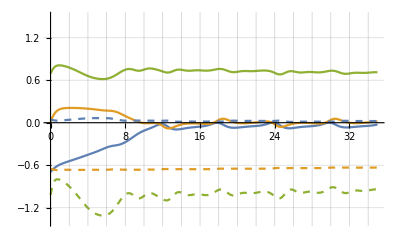
-Graphics--Graphics--Graphics-

```mathematica
If[SIMFULLY,
Labeled[
ListLinePlot[{
Table[estimate[i][[1]]-(b/.PhysicalConstants)[[1]],{i,1,NN}],
Table[estimate[i][[2]]-(b/.PhysicalConstants)[[2]],{i,1,NN}],
Table[estimate[i][[3]]-(b/.PhysicalConstants)[[3]],{i,1,NN}],
Table[estimate[i][[4]]-(B/.PhysicalConstants)[[1]],{i,1,NN}],
Table[estimate[i][[5]]-(B/.PhysicalConstants)[[2]],{i,1,NN}],
Table[estimate[i][[6]]-(B/.PhysicalConstants)[[3]],{i,1,NN}]
},
PlotStyle-> {
{RGBColor[0.368417,0.506779,0.709798]},
{RGBColor[0.880722,0.611041,0.142051]},
{RGBColor[0.560181,0.691569,0.194885]},
{RGBColor[0.368417,0.506779,0.709798], Dashed},
{RGBColor[0.880722,0.611041,0.142051], Dashed},
{RGBColor[0.560181,0.691569,0.194885], Dashed}
},
PlotLegends->Placed[LineLegend[
{
MaTeX["\\langle e_{1}, \\hat{d}_{\\scriptscriptstyle{T}}(t) - d\\rangle"],
MaTeX["\\langle e_{2}, \\hat{d}_{\\scriptscriptstyle{T}}(t) - d\\rangle"],
MaTeX["\\langle e_{3}, \\hat{d}_{\\scriptscriptstyle{T}}(t) - d\\rangle"],
MaTeX["\\langle e_{1}, \\hat{D}_{\\scriptscriptstyle{T}}(t) - D\\rangle"],
MaTeX["\\langle e_{2}, \\hat{D}_{\\scriptscriptstyle{T}}(t) - D\\rangle"],
MaTeX["\\langle e_{3}, \\hat{D}_{\\scriptscriptstyle{T}}(t) - D\\rangle"]
},
LegendLayout->"Row",
Spacings->0.1,
LegendMarkerSize->20
],
{0.5,0.9}
],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->{-1.4,1.5}
],
{MaTeX["\\text{Time (s)}"] ,MaTeX["\\text{(m/s/s)}"] },{Bottom,Top}
(*{MaTeX["\\text{Time (s)}"] ,MaTeX["\\text{(m/s/s)}"] },{Bottom,Left},RotateLabel->True*)
(*{MaTeX["\\text{Time (s)}"] ,MaTeX["\\text{(m/s/s)}"]},{Bottom,Left},RotateLabel->True*)
]
]
```

```mathematica
If[SIMFULLY,Export[NotebookDirectory[]<>"final_figures/sim_disturbances_T.pdf",%];]
```

## Disturbance estimates τ

```mathematica
(*(bτ,Bτ)*)
estimate[i_]:= estimatorsList[[i,{7,8,9,10,11,12}]];
```

### disturbance bT

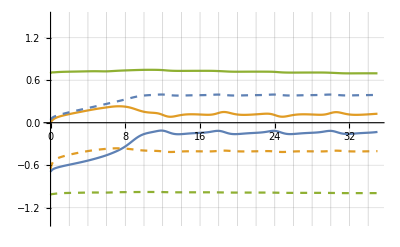
-Graphics--Graphics--Graphics-

```mathematica
If[SIMFULLY,
Labeled[
ListLinePlot[{
Table[estimate[i][[1]]-(b/.PhysicalConstants)[[1]],{i,1,NN}],
Table[estimate[i][[2]]-(b/.PhysicalConstants)[[2]],{i,1,NN}],
Table[estimate[i][[3]]-(b/.PhysicalConstants)[[3]],{i,1,NN}],
Table[estimate[i][[4]]-(B/.PhysicalConstants)[[1]],{i,1,NN}],
Table[estimate[i][[5]]-(B/.PhysicalConstants)[[2]],{i,1,NN}],
Table[estimate[i][[6]]-(B/.PhysicalConstants)[[3]],{i,1,NN}]
},
PlotStyle-> {
{RGBColor[0.368417,0.506779,0.709798]},
{RGBColor[0.880722,0.611041,0.142051]},
{RGBColor[0.560181,0.691569,0.194885]},
{RGBColor[0.368417,0.506779,0.709798], Dashed},
{RGBColor[0.880722,0.611041,0.142051], Dashed},
{RGBColor[0.560181,0.691569,0.194885], Dashed}
},
PlotLegends->Placed[LineLegend[
{
MaTeX["\\langle e_{1}, \\hat{d}_{\\scriptscriptstyle{\\tau}}(t) - d\\rangle"],
MaTeX["\\langle e_{2}, \\hat{d}_{\\scriptscriptstyle{\\tau}}(t) - d\\rangle"],
MaTeX["\\langle e_{3}, \\hat{d}_{\\scriptscriptstyle{\\tau}}(t) - d\\rangle"],
MaTeX["\\langle e_{1}, \\hat{D}_{\\scriptscriptstyle{\\tau}}(t) - D\\rangle"],
MaTeX["\\langle e_{2}, \\hat{D}_{\\scriptscriptstyle{\\tau}}(t) - D\\rangle"],
MaTeX["\\langle e_{3}, \\hat{D}_{\\scriptscriptstyle{\\tau}}(t) - D\\rangle"]
},
LegendLayout->"Row",
Spacings->0.1,
LegendMarkerSize->20
],
{0.5,0.9}
],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->{-1.4,1.5}
],
{MaTeX["\\text{Time (s)}"] ,MaTeX["\\text{(m/s/s)}"] },{Bottom,Top}
(*{MaTeX["\\text{Time (s)}"] ,MaTeX["\\text{(m/s/s)}"] },{Bottom,Left},RotateLabel->True*)
(*{MaTeX["\\text{Time (s)}"] ,MaTeX["\\text{(m/s/s)}"]},{Bottom,Left},RotateLabel->True*)
]
]
```

```mathematica
If[SIMFULLY,Export[NotebookDirectory[]<>"final_figures/sim_disturbances_tau.pdf",%];]
```

## Error position

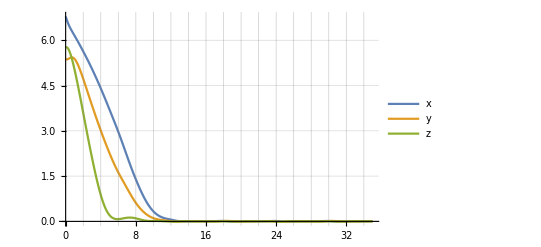
-Graphics-time (s)position error(m)

```mathematica
errorp:= stateList[[1;;NN,{1,2,3}]]-Table[pd[stepsize (i-1)],{i,1,Length[stateList[[;;,1]]]}];
If[SIMFULLY,
Labeled[
ListLinePlot[{
errorp[[;;,1]],errorp[[;;,2]],errorp[[;;,3]]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"time (s)","position error(m)"},{Bottom,Left},RotateLabel->True
]
]
```

## Error velocity

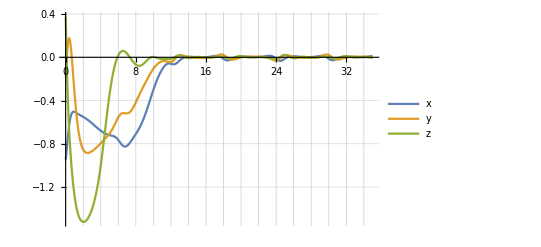
-Graphics-time (s)error(m/s)

```mathematica
errorv:= stateList[[1;;NN,{7,8,9}]]-Table[vd[stepsize (i-1)],{i,1,Length[stateList[[;;,1]]]}];
If[SIMFULLY,
Labeled[
ListLinePlot[{
errorv[[;;,1]],errorv[[;;,2]],errorv[[;;,3]]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"time (s)","error(m/s)"},{Bottom,Left},RotateLabel->True
]
]
```

## Disturbance estimates

```mathematica
(*(bT,BT)*)
estimate[i_]:= estimatorsList[[i,{1,2,3,4,5,6}]];
```

### disturbance bT

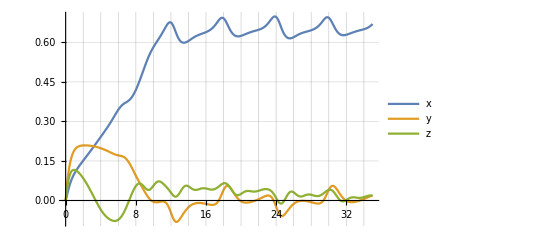
-Graphics-time (s)estimate b_T(N/kg)

```mathematica
If[SIMFULLY,
Labeled[
ListLinePlot[{
Table[estimate[i][[1]],{i,1,NN}],
Table[estimate[i][[2]],{i,1,NN}],
Table[estimate[i][[3]],{i,1,NN}]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"time (s)","estimate b_T(N/kg)"},{Bottom,Left},RotateLabel->True
]
]
```

#### note that b != bT

```mathematica
b/.PhysicalConstants
If[SIMFULLY,√(#.#)&[b-estimate[-1][[1;;3]]/.PhysicalConstants]]
If[SIMFULLY,180/π ArcCos[(#/(√(#.#))&[gravity{0,0,1}+ad[NN stepsize]-b]).(#/(√(#.#))&[gravity{0,0,1}+ad[NN stepsize]-estimate[-1][[1;;3]]])]/.PhysicalConstants]
```

{0.693672,0.,-0.693672}

0.712992

0.25515

### disturbance BT

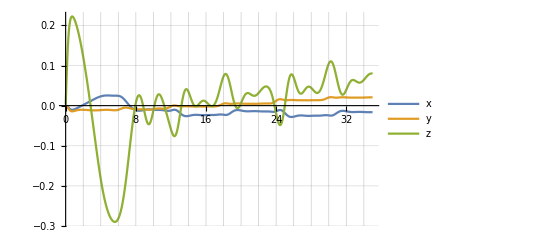
-Graphics-time (s)estimate B_T(N/kg)

```mathematica
If[SIMFULLY,
Labeled[
ListLinePlot[{
Table[estimate[i][[4]],{i,1,NN}],
Table[estimate[i][[5]],{i,1,NN}],
Table[estimate[i][[6]],{i,1,NN}]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"time (s)","estimate B_T(N/kg)"},{Bottom,Left},RotateLabel->True
]
]
```

### note that B != BT

```mathematica
B/.PhysicalConstants
If[SIMFULLY,√(#.#)&[B-estimate[-1][[4;;6]]/.PhysicalConstants]]
If[SIMFULLY,
(#1.#2&[B-estimate[-1][[4;;6]],# ]/.PhysicalConstants)&[
ϕT[f[stateList[[-1,;;]],{pd[NN stepsize],vd[NN stepsize]}][[7;;9]]]/.PhysicalConstants
]
]
```

{-0.0396718,0.654,1.02067}

1.13478

0.696643

## Disturbance estimates

```mathematica
(*(bτ,Bτ)*)
estimate[i_]:= estimatorsList[[i,{7,8,9,10,11,12}]];
```

### disturbance bτ

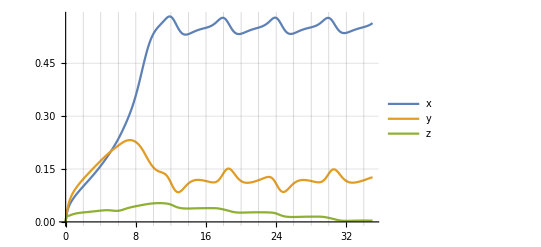
-Graphics-time (s)estimate b_τ(N/kg)

```mathematica
If[SIMFULLY,
Labeled[
ListLinePlot[{
Table[estimate[i][[1]],{i,1,NN}],
Table[estimate[i][[2]],{i,1,NN}],
Table[estimate[i][[3]],{i,1,NN}]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"time (s)","estimate b_τ(N/kg)"},{Bottom,Left},RotateLabel->True
]
]
```

#### note that b != bτ

```mathematica
b/.PhysicalConstants
If[SIMFULLY,√(#.#)&[b-estimate[-1][[1;;3]]/.PhysicalConstants]]
If[SIMFULLY,180/π ArcCos[(#/(√(#.#))&[gravity{0,0,1}+ad[NN stepsize]-b]).(#/(√(#.#))&[gravity{0,0,1}+ad[NN stepsize]-estimate[-1][[1;;3]]])]/.PhysicalConstants]
```

{0.693672,0.,-0.693672}

0.720474

1.1337

### disturbance Bτ

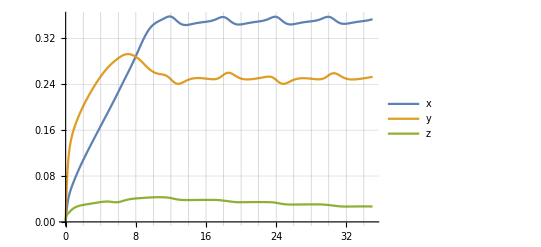
-Graphics-time (s)estimate B_τ(N/kg)

```mathematica
If[SIMFULLY,
Labeled[
ListLinePlot[{
Table[estimate[i][[4]],{i,1,NN}],
Table[estimate[i][[5]],{i,1,NN}],
Table[estimate[i][[6]],{i,1,NN}]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"time (s)","estimate B_τ(N/kg)"},{Bottom,Left},RotateLabel->True
]
]
```

#### note that B != Bτ

```mathematica
B/.PhysicalConstants
If[SIMFULLY,√(#.#)&[B-estimate[-1][[4;;6]]/.PhysicalConstants]]
If[SIMFULLY,
(#1.#2&[B-estimate[-1][[4;;6]],# ]/.PhysicalConstants)&[
ϕT[f[stateList[[-1,;;]],{pd[NN stepsize],vd[NN stepsize]}][[7;;9]]]/.PhysicalConstants
]
]
```

{-0.0396718,0.654,1.02067}

1.14159

0.725732

## Input

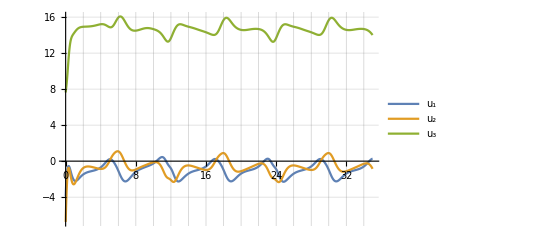
-Graphics-Time (s)(N)

```mathematica
If[SIMFULLY,
Labeled[
ListLinePlot[{
inputList[[;;,1]],
inputList[[;;,2]],
inputList[[;;,3]]
},
PlotLegends->Placed[{"u_1","u_2","u_3"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"Time (s)","(N)"},{Bottom,Left},RotateLabel->True
]
]
```

## Error in state (|z-z^*|) and in input (|u-u^*|)

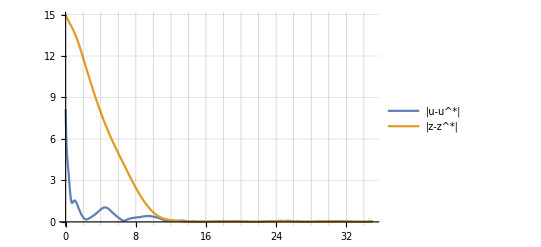
-Graphics-Time (s)

```mathematica
If[SIMFULLY,
Labeled[
ListLinePlot[{
Map[Norm,inputList-inputStarList],
Map[Norm,stateList-stateStarList]
},
PlotLegends->Placed[{"|u-u^*|","|z-z^*|"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"Time (s)",""},{Bottom,Left},RotateLabel->True
]
]
```

## Lyapunov function

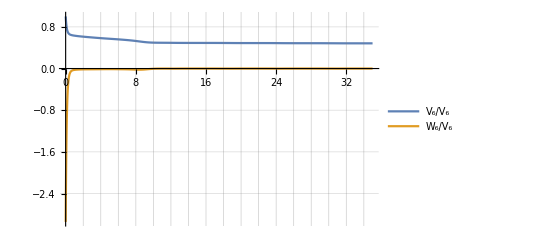
-Graphics-Time (s)

```mathematica
If[SIMFULLY,
Labeled[
ListLinePlot[{
VList/VList[[1]],
WList/VList[[1]]
},
PlotLegends->Placed[{"V_6/V_6","W_6/V_6"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"Time (s)",""},{Bottom,Left},RotateLabel->True
]
]
```

## Tension function

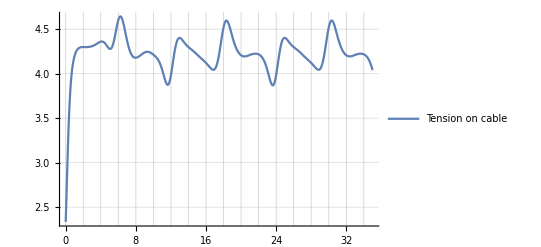
-Graphics-Time (s)(N)

```mathematica
If[SIMFULLY,
Labeled[
ListLinePlot[{
tensionsList
},
PlotLegends->Placed[{"Tension on cable"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{"Time (s)","(N)"},{Bottom,Left},RotateLabel->True
]
]
```

# model mismatch

## simulation

```mathematica
Module[{},
Clear[SIMNOTPERFECTMODEL,FASTTRAJECTORY,ESTIMATESENSITIVITY,SIMTIMEVARYINGWIND,ESTIMATESENSITIVITY2,FASTTRAJECTORY2];
If[#==1,
(*option 1*)
nameSIM="default"
];
If[#==2,
(*option 2*)
SIMNOTPERFECTMODEL=True;
nameSIM="model mismatch";
];
If[#==3,
(*option 3*)
FASTTRAJECTORY=True;
nameSIM="fast trajectory";
];
If[#==4,
(*option 4*)
ESTIMATESENSITIVITY=True;
nameSIM="estimate sensitivity";
];

If[#==5,
(*option 5*)
SIMTIMEVARYINGWIND=True;
nameSIM="time varying wind";
];

If[#==6,
(*option 6*)
ESTIMATESENSITIVITY2=True;
nameSIM="estimate sensitivity 2";
];

If[#==7,
(*option 7*)
FASTTRAJECTORY2=True;
nameSIM="fast trajectory 2";
];
]&[2]
nameSIM
```

model mismatch

```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"model_and_change_of_coordinates.nb"}]]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"backstepping_steps.nb"}]]
(*Play[Sin[440 2Pi t],{t,0,1}](*Beep[]*)*)
```

## Import

```mathematica
stateList=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_state.mx"];
estimatorsList=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_estimators.mx"];inputList=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_input.mx"];
stateStarList=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_statestar.mx"];
inputStarList=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_inputstar.mx"];
tensionsList=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_tension.mx"];
VList=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_V.mx"];
WList=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_W.mx"];
```

## some important data

```mathematica
stepsize=0.005;
TFINAL=35;
NN=Length[stateList];
XTicksLabels=Table[{Round[1/stepsize]i+1,i},{i,0,TFINAL,2}];
```

## position error, state error and disturbances

```mathematica
errorp:= stateList[[1;;NN,{1,2,3}]]-Table[pd[stepsize (i-1)],{i,1,Length[stateList[[;;,1]]]}];
(*(bT,BT)*)
estimate[i_]:= estimatorsList[[i,{1,2,3,4,5,6}]];
```

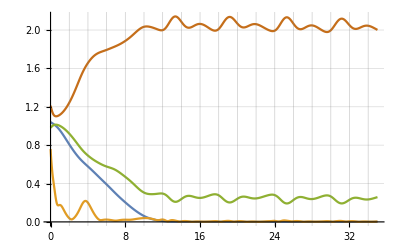
-Graphics--Graphics-

```mathematica
If[SIMFULLY,
Labeled[
ListLinePlot[{
Map[Norm,errorp]/10,
Map[Norm,inputList-inputStarList]/10,
Table[Norm[estimate[i][[1;;3]]-(b/.PhysicalConstants)],{i,1,NN}],
Table[Norm[estimate[i][[4;;6]]-(B/.PhysicalConstants)],{i,1,NN}]
},
PlotStyle-> {
{RGBColor[0.368417,0.506779,0.709798]},
{RGBColor[0.880722,0.611041,0.142051]},
{RGBColor[0.560181,0.691569,0.194885]},
{RGBColor[0.772079,0.431554,0.102387]}
},
PlotLegends->Placed[LineLegend[Automatic,
{
MaTeX["\\frac{1}{10}\\| p^{\\scriptscriptstyle{(0)}}(t) - p_{\\star}^{\\scriptscriptstyle{(0)}}(t) \\| \\text{(m)}"],
MaTeX["\\frac{1}{10}\\| z(t) - z_{\\star +}(t) \\|"],
MaTeX["\\| \\hat{d}_{\\scriptscriptstyle{T}}(t) - d \\| \\text{(m/s/s)}"],
MaTeX["\\| \\hat{D}_{\\scriptscriptstyle{T}}(t) - D \\| \\text{(m/s/s)}"]
},
Spacings->0.2],
{0.8,0.6}
],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{MaTeX["\\text{Time (s)}"]},{Bottom,Left},RotateLabel->True
]
]
```

```mathematica
If[SIMFULLY,Export[NotebookDirectory[]<>"final_figures/sim_model_mismatch.pdf",%];]
```

# excitation vs convergence

## simulation

```mathematica
Module[{},
Clear[SIMNOTPERFECTMODEL,FASTTRAJECTORY,ESTIMATESENSITIVITY,SIMTIMEVARYINGWIND,ESTIMATESENSITIVITY2,FASTTRAJECTORY2];
If[#==1,
(*option 1*)
nameSIM="default"
];
If[#==2,
(*option 2*)
SIMNOTPERFECTMODEL=True;
nameSIM="model mismatch";
];
If[#==3,
(*option 3*)
FASTTRAJECTORY=True;
nameSIM="fast trajectory";
];
If[#==4,
(*option 4*)
ESTIMATESENSITIVITY=True;
nameSIM="estimate sensitivity";
];

If[#==5,
(*option 5*)
SIMTIMEVARYINGWIND=True;
nameSIM="time varying wind";
];

If[#==6,
(*option 6*)
ESTIMATESENSITIVITY2=True;
nameSIM="estimate sensitivity 2";
];

If[#==7,
(*option 7*)
FASTTRAJECTORY2=True;
nameSIM="fast trajectory 2";
];
]&[1]
nameSIM
```

default

```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"model_and_change_of_coordinates.nb"}]]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"backstepping_steps.nb"}]]
(*Play[Sin[440 2Pi t],{t,0,1}](*Beep[]*)*)
```

## Import

```mathematica
stateList1=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_state.mx"];
estimatorsList1=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_estimators.mx"];inputList1=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_input.mx"];
stateStarList1=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_statestar.mx"];
inputStarList1=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_inputstar.mx"];
tensionsList1=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_tension.mx"];
VList1=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_V.mx"];
WList1=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_W.mx"];
```

## simulation

```mathematica
Module[{},
Clear[SIMNOTPERFECTMODEL,FASTTRAJECTORY,ESTIMATESENSITIVITY,SIMTIMEVARYINGWIND,ESTIMATESENSITIVITY2,FASTTRAJECTORY2];
If[#==1,
(*option 1*)
nameSIM="default"
];
If[#==2,
(*option 2*)
SIMNOTPERFECTMODEL=True;
nameSIM="model mismatch";
];
If[#==3,
(*option 3*)
FASTTRAJECTORY=True;
nameSIM="fast trajectory";
];
If[#==4,
(*option 4*)
ESTIMATESENSITIVITY=True;
nameSIM="estimate sensitivity";
];

If[#==5,
(*option 5*)
SIMTIMEVARYINGWIND=True;
nameSIM="time varying wind";
];

If[#==6,
(*option 6*)
ESTIMATESENSITIVITY2=True;
nameSIM="estimate sensitivity 2";
];

If[#==7,
(*option 7*)
FASTTRAJECTORY2=True;
nameSIM="fast trajectory 2";
];
]&[3]
nameSIM
```

fast trajectory

```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"model_and_change_of_coordinates.nb"}]]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"backstepping_steps.nb"}]]
(*Play[Sin[440 2Pi t],{t,0,1}](*Beep[]*)*)
```

## Import

```mathematica
stateList2=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_state.mx"];
estimatorsList2=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_estimators.mx"];inputList2=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_input.mx"];
stateStarList2=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_statestar.mx"];
inputStarList2=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_inputstar.mx"];
tensionsList2=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_tension.mx"];
VList2=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_V.mx"];
WList2=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_W.mx"];
```

## simulation

```mathematica
Module[{},
Clear[SIMNOTPERFECTMODEL,FASTTRAJECTORY,ESTIMATESENSITIVITY,SIMTIMEVARYINGWIND,ESTIMATESENSITIVITY2,FASTTRAJECTORY2];
If[#==1,
(*option 1*)
nameSIM="default"
];
If[#==2,
(*option 2*)
SIMNOTPERFECTMODEL=True;
nameSIM="model mismatch";
];
If[#==3,
(*option 3*)
FASTTRAJECTORY=True;
nameSIM="fast trajectory";
];
If[#==4,
(*option 4*)
ESTIMATESENSITIVITY=True;
nameSIM="estimate sensitivity";
];

If[#==5,
(*option 5*)
SIMTIMEVARYINGWIND=True;
nameSIM="time varying wind";
];

If[#==6,
(*option 6*)
ESTIMATESENSITIVITY2=True;
nameSIM="estimate sensitivity 2";
];

If[#==7,
(*option 7*)
FASTTRAJECTORY2=True;
nameSIM="fast trajectory 2";
];
]&[7]
nameSIM
```

fast trajectory 2

```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"model_and_change_of_coordinates.nb"}]]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"backstepping_steps.nb"}]]
(*Play[Sin[440 2Pi t],{t,0,1}](*Beep[]*)*)
```

## Import

```mathematica
stateList3=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_state.mx"];
estimatorsList3=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_estimators.mx"];inputList3=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_input.mx"];
stateStarList3=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_statestar.mx"];
inputStarList3=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_inputstar.mx"];
tensionsList3=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_tension.mx"];
VList3=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_V.mx"];
WList3=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_W.mx"];
```

## some important data

```mathematica
stepsize=0.005;
TFINAL=35;
NN=Length[stateList1];
XTicksLabels=Table[{Round[1/stepsize]i+1,i},{i,0,TFINAL,2}];
```

## disturbance estimates errors

```mathematica
(*(bT,BT)*)
estimate1[i_]:= estimatorsList1[[i,{1,2,3,4,5,6}]];
estimate2[i_]:= estimatorsList2[[i,{1,2,3,4,5,6}]];
estimate3[i_]:= estimatorsList3[[i,{1,2,3,4,5,6}]];
```

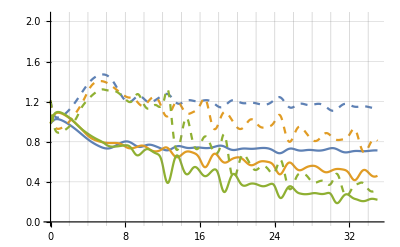
-Graphics--Graphics--Graphics-

```mathematica
If[SIMFULLY,
Labeled[
ListLinePlot[{
Table[Norm[estimate1[i][[1;;3]]-(b/.PhysicalConstants)],{i,1,NN}],
Table[Norm[estimate1[i][[4;;6]]-(B/.PhysicalConstants)],{i,1,NN}],
Table[Norm[estimate2[i][[1;;3]]-(b/.PhysicalConstants)],{i,1,NN}],
Table[Norm[estimate2[i][[4;;6]]-(B/.PhysicalConstants)],{i,1,NN}],
Table[Norm[estimate3[i][[1;;3]]-(b/.PhysicalConstants)],{i,1,NN}],
Table[Norm[estimate3[i][[4;;6]]-(B/.PhysicalConstants)],{i,1,NN}]
},
PlotStyle-> {
{RGBColor[0.368417,0.506779,0.709798]},
{RGBColor[0.368417,0.506779,0.709798],Dashed},
{RGBColor[0.880722,0.611041,0.142051]},
{RGBColor[0.880722,0.611041,0.142051],Dashed},
{RGBColor[0.560181,0.691569,0.194885]},
{RGBColor[0.560181,0.691569,0.194885],Dashed}
},
PlotLegends->Placed[LineLegend[
{
MaTeX["\\| \\hat{d}_{\\scriptscriptstyle{T}}(t) - d \\| , \\omega= 2\\pi/12"],
MaTeX["\\| \\hat{D}_{\\scriptscriptstyle{T}}(t) - D \\| , \\omega= 2\\pi/12"],
MaTeX["\\| \\hat{d}_{\\scriptscriptstyle{T}}(t) - d \\| , \\omega= 2\\pi/8\\hphantom{0}"],
MaTeX["\\| \\hat{D}_{\\scriptscriptstyle{T}}(t) - D \\| , \\omega= 2\\pi/8\\hphantom{0}"],
MaTeX["\\| \\hat{d}_{\\scriptscriptstyle{T}}(t) - d \\| , \\omega= 2\\pi/6\\hphantom{0}"],
MaTeX["\\| \\hat{D}_{\\scriptscriptstyle{T}}(t) - D \\| , \\omega= 2\\pi/6\\hphantom{0}"]
},
LegendLayout->{"Row",3},
(*LegendMarkerSize->20,*)
Spacings->0.2],
{0.5,0.87}
],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->{0,2.05}
],
{MaTeX["\\text{Time (s)}"],MaTeX["\\text{(m/s/s)}"]},{Bottom,Top}
]
]
```

```mathematica
If[SIMFULLY,Export[NotebookDirectory[]<>"final_figures/sim_excitation_vs_convergence.pdf",%];]
```

# sensitivity to initial conditions: disturbance estimate

## simulation

```mathematica
Module[{},
Clear[SIMNOTPERFECTMODEL,FASTTRAJECTORY,ESTIMATESENSITIVITY,SIMTIMEVARYINGWIND,ESTIMATESENSITIVITY2,FASTTRAJECTORY2];
If[#==1,
(*option 1*)
nameSIM="default"
];
If[#==2,
(*option 2*)
SIMNOTPERFECTMODEL=True;
nameSIM="model mismatch";
];
If[#==3,
(*option 3*)
FASTTRAJECTORY=True;
nameSIM="fast trajectory";
];
If[#==4,
(*option 4*)
ESTIMATESENSITIVITY=True;
nameSIM="estimate sensitivity";
];

If[#==5,
(*option 5*)
SIMTIMEVARYINGWIND=True;
nameSIM="time varying wind";
];

If[#==6,
(*option 6*)
ESTIMATESENSITIVITY2=True;
nameSIM="estimate sensitivity 2";
];

If[#==7,
(*option 7*)
FASTTRAJECTORY2=True;
nameSIM="fast trajectory 2";
];
]&[4]
nameSIM
```

estimate sensitivity

```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"model_and_change_of_coordinates.nb"}]]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"backstepping_steps.nb"}]]
(*Play[Sin[440 2Pi t],{t,0,1}](*Beep[]*)*)
```

```mathematica
dTBound1= θ0bT+ϵBT/.ControllersWithEstimators;
DTBound1 =θ0BT+ϵBT/.ControllersWithEstimators;
dBound1=θ0bT/.ControllersWithEstimators;
DBound1=θ0BT/.ControllersWithEstimators;
```

## Import

```mathematica
stateList1=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_state.mx"];
estimatorsList1=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_estimators.mx"];inputList1=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_input.mx"];
stateStarList1=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_statestar.mx"];
inputStarList1=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_inputstar.mx"];
tensionsList1=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_tension.mx"];
VList1=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_V.mx"];
WList1=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_W.mx"];
```

## simulation

```mathematica
Module[{},
Clear[SIMNOTPERFECTMODEL,FASTTRAJECTORY,ESTIMATESENSITIVITY,SIMTIMEVARYINGWIND,ESTIMATESENSITIVITY2,FASTTRAJECTORY2];
If[#==1,
(*option 1*)
nameSIM="default"
];
If[#==2,
(*option 2*)
SIMNOTPERFECTMODEL=True;
nameSIM="model mismatch";
];
If[#==3,
(*option 3*)
FASTTRAJECTORY=True;
nameSIM="fast trajectory";
];
If[#==4,
(*option 4*)
ESTIMATESENSITIVITY=True;
nameSIM="estimate sensitivity";
];

If[#==5,
(*option 5*)
SIMTIMEVARYINGWIND=True;
nameSIM="time varying wind";
];

If[#==6,
(*option 6*)
ESTIMATESENSITIVITY2=True;
nameSIM="estimate sensitivity 2";
];

If[#==7,
(*option 7*)
FASTTRAJECTORY2=True;
nameSIM="fast trajectory 2";
];
]&[6]
nameSIM
```

estimate sensitivity 2

```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"model_and_change_of_coordinates.nb"}]]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"backstepping_steps.nb"}]]
(*Play[Sin[440 2Pi t],{t,0,1}](*Beep[]*)*)
```

```mathematica
dTBound2= θ0bT+ϵBT/.ControllersWithEstimators;
DTBound2 =θ0BT+ϵBT/.ControllersWithEstimators;
dBound2=θ0bT/.ControllersWithEstimators;
DBound2=θ0BT/.ControllersWithEstimators;
```

## Import

```mathematica
stateList2=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_state.mx"];
estimatorsList2=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_estimators.mx"];inputList2=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_input.mx"];
stateStarList2=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_statestar.mx"];
inputStarList2=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_inputstar.mx"];
tensionsList2=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_tension.mx"];
VList2=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_V.mx"];
WList2=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_W.mx"];
```

## simulation

```mathematica
Module[{},
Clear[SIMNOTPERFECTMODEL,FASTTRAJECTORY,ESTIMATESENSITIVITY,SIMTIMEVARYINGWIND,ESTIMATESENSITIVITY2,FASTTRAJECTORY2];
If[#==1,
(*option 1*)
nameSIM="default"
];
If[#==2,
(*option 2*)
SIMNOTPERFECTMODEL=True;
nameSIM="model mismatch";
];
If[#==3,
(*option 3*)
FASTTRAJECTORY=True;
nameSIM="fast trajectory";
];
If[#==4,
(*option 4*)
ESTIMATESENSITIVITY=True;
nameSIM="estimate sensitivity";
];

If[#==5,
(*option 5*)
SIMTIMEVARYINGWIND=True;
nameSIM="time varying wind";
];

If[#==6,
(*option 6*)
ESTIMATESENSITIVITY2=True;
nameSIM="estimate sensitivity 2";
];

If[#==7,
(*option 7*)
FASTTRAJECTORY2=True;
nameSIM="fast trajectory 2";
];

If[#==8,
(*option 6*)
ESTIMATESENSITIVITY3=True;
nameSIM="estimate sensitivity 3";
];
]&[8]
nameSIM
```

estimate sensitivity 3

```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"model_and_change_of_coordinates.nb"}]]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"backstepping_steps.nb"}]]
(*Play[Sin[440 2Pi t],{t,0,1}](*Beep[]*)*)
```

```mathematica
dTBound3= θ0bT+ϵbT/.ControllersWithEstimators;
DTBound3=θ0BT+ϵBT/.ControllersWithEstimators;
dBound3=θ0bT/.ControllersWithEstimators;
DBound3=θ0BT/.ControllersWithEstimators;
```

## Import

```mathematica
stateList3=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_state.mx"];
estimatorsList3=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_estimators.mx"];inputList3=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_input.mx"];
stateStarList3=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_statestar.mx"];
inputStarList3=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_inputstar.mx"];
tensionsList3=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_tension.mx"];
VList3=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_V.mx"];
WList3=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_W.mx"];
```

## some important data

```mathematica
stepsize=0.005;
TFINAL=35;
NN=Length[stateList1];
(*NN=Length[stateList2];*)
XTicksLabels=Table[{Round[1/stepsize]i+1,i},{i,0,TFINAL,2}];
```

## disturbance estimates norms

```mathematica
(*(bT,BT)*)
estimate1[i_]:= estimatorsList1[[i,{1,2,3,4,5,6}]];
estimate2[i_]:= estimatorsList2[[i,{1,2,3,4,5,6}]];
estimate3[i_]:= estimatorsList3[[i,{1,2,3,4,5,6}]];
```

```mathematica
dBound1
DBound1
```

1.2

1.5

```mathematica
dTBound1
dTBound2
dTBound3
```

1.5

1.5

1.5

```mathematica
DTBound1
DTBound2
DTBound3
```

1.8

1.8

1.8

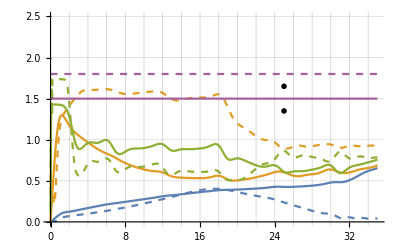
-Graphics--Graphics--Graphics-

```mathematica
If[SIMFULLY,
Labeled[
ListLinePlot[
{
Table[Norm[estimate1[i][[1;;3]]],{i,1,NN}],
Table[Norm[estimate1[i][[4;;6]]],{i,1,NN}],
Table[Norm[estimate2[i][[1;;3]]],{i,1,NN}],
Table[Norm[estimate2[i][[4;;6]]],{i,1,NN}],
Table[Norm[estimate3[i][[1;;3]]],{i,1,NN}],
Table[Norm[estimate3[i][[4;;6]]],{i,1,NN}],
Table[dTBound1,{i,1,NN}],
Table[DTBound1,{i,1,NN}](*,*)
(*Table[dBound1,{i,1,NN}],*)
(*Table[DBound1,{i,1,NN}]*)
},
Epilog->{
{Text[MaTeX["\\bar{\\hat{d}}_{\\scriptscriptstyle{T}} = 1.5 \\text{ and } \\bar{d}_{\\scriptscriptstyle{T}} = 1.2 \\text{ and } \\| d \\| \\approx 0.98"],{5000,dTBound1-0.15}],RGBColor[0.647624,0.37816,0.614037]},
{Text[MaTeX["\\bar{\\hat{D}}_{\\scriptscriptstyle{T}} = 1.8 \\text{ and } \\bar{D}_{\\scriptscriptstyle{T}} = 1.5 \\text{ and } \\| D \\| \\approx 1.21"],{5000,DTBound1-0.15}],RGBColor[0.647624,0.37816,0.614037]}
(*(*{PointSize[Medium],Point[{1,dTBound1}]},*)
{Text[MaTeX["\\bar{\\hat{d}}_{\\scriptscriptstyle{T}} = 1.5"],{600,dTBound1-0.15}],RGBColor[0.647624,0.37816,0.614037]},
(*{PointSize[Medium],Point[{1,DTBound1}]},*)
{Text[MaTeX["\\bar{\\hat{D}}_{\\scriptscriptstyle{T}} = 1.8"],{600,DTBound1-0.15}],RGBColor[0.647624,0.37816,0.614037]},
(*{PointSize[Medium],Point[{1,dBound1}]},*)
{Text[MaTeX["\\bar{d}_{\\scriptscriptstyle{T}} = 1.2"],{600,dBound1-0.15}],RGBColor[0.915,0.3325,0.2125]},
(*{PointSize[Medium],Point[{1,DBound1}]},*)
{Text[MaTeX["\\bar{D}_{\\scriptscriptstyle{T}} = 1.5"],{600,DBound1-0.15}],RGBColor[0.915,0.3325,0.2125]}*)
},
PlotStyle-> {
{RGBColor[0.368417,0.506779,0.709798]},
{RGBColor[0.368417,0.506779,0.709798],Dashed},
{RGBColor[0.880722,0.611041,0.142051]},
{RGBColor[0.880722,0.611041,0.142051],Dashed},
{RGBColor[0.560181,0.691569,0.194885]},
{RGBColor[0.560181,0.691569,0.194885],Dashed},
{RGBColor[0.647624,0.37816,0.614037]},
{RGBColor[0.647624,0.37816,0.614037],Dashed},
{RGBColor[0.915,0.3325,0.2125]},
{RGBColor[0.915,0.3325,0.2125],Dashed}
},
PlotLegends->Placed[LineLegend[
{MaTeX["\\| \\hat{d}_{\\scriptscriptstyle{T}}(t) \\| , V_{\\scriptscriptstyle{1,0}}=V_{\\scriptscriptstyle{2,0}}=2\\hphantom{00}"],
MaTeX["\\| \\hat{D}_{\\scriptscriptstyle{T}}(t) \\| , V_{\\scriptscriptstyle{1,0}}=V_{\\scriptscriptstyle{2,0}}=2\\hphantom{00}"],
MaTeX["\\| \\hat{d}_{\\scriptscriptstyle{T}}(t) \\| , V_{\\scriptscriptstyle{1,0}}=V_{\\scriptscriptstyle{2,0}}=20\\hphantom{0}"],
MaTeX["\\| \\hat{D}_{\\scriptscriptstyle{T}}(t) \\| , V_{\\scriptscriptstyle{1,0}}=V_{\\scriptscriptstyle{2,0}}=20\\hphantom{0}"],
MaTeX["\\| \\hat{d}_{\\scriptscriptstyle{T}}(t) \\| , V_{\\scriptscriptstyle{1,0}}=V_{\\scriptscriptstyle{2,0}}=200"],
MaTeX["\\| \\hat{D}_{\\scriptscriptstyle{T}}(t) \\| , V_{\\scriptscriptstyle{1,0}}=V_{\\scriptscriptstyle{2,0}}=200"]
(*,
MaTeX["\\bar{\\hat{d}}_{\\scriptscriptstyle{T}} \\hphantom{aaaaaaaaaaaaaaaaa}"],
MaTeX["\\bar{\\hat{D}}_{\\scriptscriptstyle{T}} \\hphantom{aaaaaaaaaaaaaaaaa}"]*)
},
LegendLayout->{"Row",3},
LegendMarkerSize->21,
Spacings->0.03],
{0.5,0.86}
],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->{0,2.5}
],
{MaTeX["\\text{Time (s)}"],MaTeX["\\text{(m/s/s)}"]},{Bottom,Top}
]
]
```

```mathematica
If[SIMFULLY,Export[NotebookDirectory[]<>"final_figures/sim_sensitivity_to_initial_conditions.pdf",%];]
```

```mathematica
Norm[b]/.PhysicalConstants
Norm[B]/.PhysicalConstants
```

0.981

1.21287

# time-varying wind

## simulation

```mathematica
Module[{},
Clear[SIMNOTPERFECTMODEL,FASTTRAJECTORY,ESTIMATESENSITIVITY,SIMTIMEVARYINGWIND,ESTIMATESENSITIVITY2,FASTTRAJECTORY2];
If[#==1,
(*option 1*)
nameSIM="default"
];
If[#==2,
(*option 2*)
SIMNOTPERFECTMODEL=True;
nameSIM="model mismatch";
];
If[#==3,
(*option 3*)
FASTTRAJECTORY=True;
nameSIM="fast trajectory";
];
If[#==4,
(*option 4*)
ESTIMATESENSITIVITY=True;
nameSIM="estimate sensitivity";
];

If[#==5,
(*option 5*)
SIMTIMEVARYINGWIND=True;
nameSIM="time varying wind";
];

If[#==6,
(*option 6*)
ESTIMATESENSITIVITY2=True;
nameSIM="estimate sensitivity 2";
];

If[#==7,
(*option 7*)
FASTTRAJECTORY2=True;
nameSIM="fast trajectory 2";
];
]&[5]
nameSIM
```

time varying wind

```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"model_and_change_of_coordinates.nb"}]]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"backstepping_steps.nb"}]]
(*Play[Sin[440 2Pi t],{t,0,1}](*Beep[]*)*)
```

## Import

```mathematica
stateList=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_state.mx"];
estimatorsList=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_estimators.mx"];inputList1=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_input.mx"];
stateStarList=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_statestar.mx"];
inputStarList=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_inputstar.mx"];
tensionsList=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_tension.mx"];
VList=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_V.mx"];
WList=Import[NotebookDirectory[]<>"figures/fullyactuated/"<>nameSIM<>"/data_W.mx"];
```

## some important data

```mathematica
stepsize=0.005;
TFINAL=35;
NN=Length[stateList];
XTicksLabels=Table[{Round[1/stepsize]i+1,i},{i,0,TFINAL,2}];
```

## position error, state error and disturbances

```mathematica
errorp:= stateList[[1;;NN,{1,2,3}]]-Table[pd[stepsize (i-1)],{i,1,Length[stateList[[;;,1]]]}];
(*(bT,BT)*)
estimate[i_]:= estimatorsList[[i,{1,2,3,4,5,6}]];
```

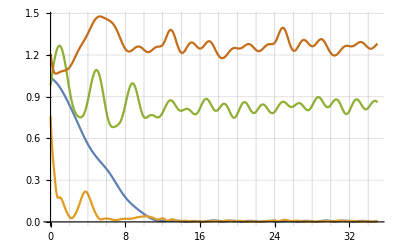
-Graphics--Graphics-

```mathematica
If[SIMFULLY,
Labeled[
ListLinePlot[{
Map[Norm,errorp]/10,
Map[Norm,inputList-inputStarList]/10,
Table[Norm[estimate[i][[1;;3]]-(({w1,w2,w3}+{0.15 Sin[(2π)/4 stepsize(i-1)],0,0})/m/.PhysicalConstants)],{i,1,NN}],
Table[Norm[estimate[i][[4;;6]]-(({W1,W2,W3}+{0.15 Sin[(2π)/4 stepsize(i-1)],0,0})/M-({w1,w2,w3}+{0.15 Sin[(2π)/4 stepsize(i-1)],0,0})/m/.PhysicalConstants)],{i,1,NN}]
},
PlotStyle-> {
{RGBColor[0.368417,0.506779,0.709798]},
{RGBColor[0.880722,0.611041,0.142051]},
{RGBColor[0.560181,0.691569,0.194885]},
{RGBColor[0.772079,0.431554,0.102387]}
},
PlotLegends->Placed[LineLegend[Automatic,
{
MaTeX["\\frac{1}{10}\\| p^{\\scriptscriptstyle{(0)}}(t) - p_{\\star}^{\\scriptscriptstyle{(0)}}(t) \\| \\text{(m)}"],
MaTeX["\\frac{1}{10}\\| z(t) - z_{\\star +}(t) \\|"],
MaTeX["\\| \\hat{d}_{\\scriptscriptstyle{T}}(t) - d(t) \\| \\text{(m/s/s)}"],
MaTeX["\\| \\hat{D}_{\\scriptscriptstyle{T}}(t) - D(t) \\| \\text{(m/s/s)}"]
},
Spacings->0.2],
{0.8,0.6}
],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{MaTeX["\\text{Time (s)}"]},{Bottom,Left},RotateLabel->True
]
]
```

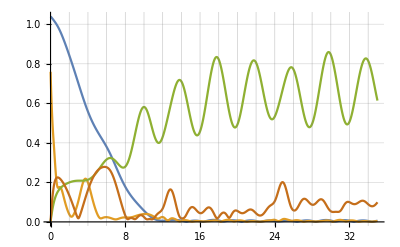
-Graphics--Graphics-

```mathematica
If[SIMFULLY,
Labeled[
ListLinePlot[{
Map[Norm,errorp]/10,
Map[Norm,inputList-inputStarList]/10,
Table[Norm[estimate[i][[1;;3]]],{i,1,NN}],
Table[Norm[estimate[i][[4;;6]]],{i,1,NN}]
},
PlotStyle-> {
{RGBColor[0.368417,0.506779,0.709798]},
{RGBColor[0.880722,0.611041,0.142051]},
{RGBColor[0.560181,0.691569,0.194885]},
{RGBColor[0.772079,0.431554,0.102387]}
},
PlotLegends->Placed[LineLegend[
{
MaTeX["\\ 0.1\\| p^{\\scriptscriptstyle{(0)}}(t) - p_{\\star}^{\\scriptscriptstyle{(0)}}(t) \\| \\text{(m)}"],
MaTeX["\\ 0.1\\| z(t) - z_{\\star +}(t) \\|"],
MaTeX["\\| \\hat{d}_{\\scriptscriptstyle{T}}(t) \\| \\text{(m/s/s)} \\hphantom{aaaaaa}"],
MaTeX["\\| \\hat{D}_{\\scriptscriptstyle{T}}(t) \| \\text{(m/s/s)}"]
},
LegendLayout->"Row",
LegendMarkerSize->25,
Spacings->0.2],
{0.5,0.9}
],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic,
PlotRange->All
],
{MaTeX["\\text{Time (s)}"]},{Bottom,Left},RotateLabel->True
]
]
```

```mathematica
If[SIMFULLY,Export[NotebookDirectory[]<>"final_figures/sim_time_varying_wind.pdf",%];]
```